## Function

```mathematica
(*以下函数参考文章“Iterative algorithm for reconstruction of entangled states”*)
StateEstimation[F_List,S_List,ϵ_:0.1,Itr1_:200,Itr2_:10]:=
Module[{cnv,dim=Length[S],tF,R,Φ,H,P,ρ,χ,G,θ},
R=ConstantArray[1,dim]/dim;(* eigenvalue *)
Φ=IdentityMatrix[dim];(* eigenstate/eigenbasis *)
tF=Total[F];
cnv=Reap[
Do[
H=Φ†.S;
Do[
P=F/Abs[Diagonal[H†.DiagonalMatrix[R].H]];(*P=(f(j))/(p(j)),p(j)=H†.DiagonalMatrix[R].H*)
R=R*(P.Abs[Hᵀ]^2/tF);(*(7),R=Subscript[r, i]*)
,{Itr2}];
R=Normalize[R,Total];
ρ=Φ.DiagonalMatrix[R].Φ†;(*(8)*)
χ=S.DiagonalMatrix[P].S†;(*(12),χ=R*)
G=ⅈ(#-#†)&[ρ.χ];(*(13)*)
θ=ϵ Abs[Tr[G.G]/Tr[G.χ.G.ρ]];(*(11),right*)
Φ=(Normalize/@(MatrixExp[ⅈ θ G].Φ)ᵀ)ᵀ;(*(9)*)
Sow[Log[Abs[Total[F (Log[P])]]],1];
Sow[Log[Abs[Tr[G.G]]],2];
Sow[Log[Abs[θ]],3];
,{Itr1}];
]⟦2⟧;
{Φ.DiagonalMatrix[R].Φ†,Max[R],cnv}
];

Fidelity[r_,s_]:=Abs[Tr[MatrixPower[MatrixPower[r,1/2].s.MatrixPower[r,1/2],1/2]]];
(*phonon annihilation operator*)
ClearAll[aOptr]
aOptr[n_]:=DiagonalMatrix[√Range[n],1];

(*displacement operator*)
ClearAll[DispOptr]
DispOptr[α_,n_]:=MatrixExp[(#†-#)&[N[α*aOptr[n]]]];


ThermalState[nb_,mn_]:=DiagonalMatrix[#/Total[#]&[Table[nb^n/(1+nb)^(n+1),{n,0,mn}]]];

MeasurmentBasis[a_,n_]:=Flatten[Table[IdentityMatrix[n+1]⟦j+1⟧.DispOptr[-a⟦i⟧,n]†,{i,1,Length[a]},{j,0,n}],1]ᵀ;

WignerFunction[ρ_,α_]:=Re[2/π Sum[(-1)^(n-1)(#†.ρ.#)&[DispOptr[α,Length[ρ]-1]]⟦n,n⟧,{n,1,Length[ρ]}]];

WignerFunctionNOPi2[ρ_,α_]:=Re[Sum[(-1)^(n-1)(#†.ρ.#)&[DispOptr[α,Length[ρ]-1]]⟦n,n⟧,{n,1,Length[ρ]}]];

DensityMatrixPlot[ρ_,func_,vpt_:1.2{3.33,-8.26,5.36}]:=BarChart3D[func[ρ],ChartLayout->"Grid",ViewPoint->vpt,BarSpacing->{Large,Medium},ChartLabels->{#,#}&[Range[Length[ρ]]-1](*,PlotRange->{All,All,{0,0.5}}*)];

WignerFunctionPlot[ρ_,maxA_,pnt_,maxn_:30,viewpointtable_:{-4.5,-8.3,4.7}]:=
Module[{dat,m},
dat=Flatten[ParallelTable[{x,p,WignerFunction[PadRight[ρ,{maxn,maxn}],x+ⅈ p]},{x,-maxA,maxA,2maxA/pnt},{p,-maxA,maxA,2maxA/pnt}],1];
m=Max[dat⟦All,3⟧];
ListPlot3D[dat,ViewPoint->viewpointtable,PlotRange->All,ColorFunction->(Hue[0.7#3/m+0.3]&),Mesh->None,ColorFunctionScaling->False]
];

WignerFunctionPlotNOPi[ρ_,maxA_,pnt_,maxn_:30,lower_:-0.3,viewpointtable_:{-4.5,-8.3,4.7}]:=
Module[{dat,m},
dat=Flatten[ParallelTable[{x,p,WignerFunctionNOPi2[PadRight[ρ,{maxn,maxn}],x+ⅈ p]},{x,-maxA,maxA,2maxA/pnt},{p,-maxA,maxA,2maxA/pnt}],1];
m=Max[dat⟦All,3⟧];
ListPlot3D[dat,ViewPoint->viewpointtable,PlotRange->{All,All,{lower,1}},ColorFunction->(Hue[0.7#3/m+0.3]&),Mesh->None,ColorFunctionScaling->False]
];
```

```mathematica
(*WignerFunctionPlot[ρ_,maxA_,pnt_,maxn_:30]:=ListPlot3D[Flatten[Table[{x,p,WignerFunction[PadRight[ρ,{maxn,maxn}],x+ⅈ p]},{x,-maxA,maxA,2maxA/pnt},{p,-maxA,maxA,2maxA/pnt}],1],ViewPoint->1.2{3.33,-8.26,5.36},PlotRange->All];*)
```

## Example

0.858859

-Graphics3D-

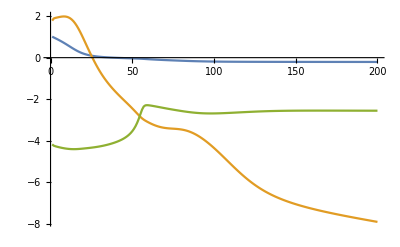

```mathematica
(* List of phonon distribution of different displaced states by blue sideband analysis *)
dat=Import[NotebookDirectory[]<>"StateEstimationExample.mat"]⟦1⟧;
(* Join them all one by one *)
F=Flatten[dat];
(* List of corresponding α of different measurements, "amp" is the displacement amplitude *)
amp=0.8;
a=Table[amp ⅇ^(2π ⅈ(i/Length[dat])),{i,0,Length[dat]-1}];
(* Max phonon number of the data *)
n=Length[dat⟦1⟧]-1;
(* Matrix of measurement basis *)
S=MeasurmentBasis[a,n];
(* Usually the default values for ϵ, Itr1 and Itr2 should be OK *)
{ρ,purity,conv}=StateEstimation[F,S];
(* purity: Purity of ρ *) 
purity
(* ρ: Density matrix, the function can be Re, Im or Abs *)
DensityMatrixPlot[ρ,Re]
(* conv: Convergence data *)
ListLinePlot[conv,PlotRange->All]
```

```mathematica
(* Wigner function of ρ, maxA: Max |α|, pnt: number of points in each dimension. MAY BE VERY SLOW. *)
WignerFunctionPlot[ρ,3,20]
```

-Graphics3D-